# Phase portraits (figures 3 and 4)

## Charlie Brummitt

## Set of strategies that could be best response

```mathematica
SetDirectory[NotebookDirectory[]];
```

Import strategiesThatCouldBeBestResponses and probSuccess:

```mathematica
Get["set_strategies_that_could_be_best_response.wl"];
```

## Figure 3

We fix the exogenous parameters α=0.1,β=0.4 and iterate over F from 0 to 1 in steps of 10^-4. For each value of F, we compute the best response from equation 4 and the ODE from equation (2b).

### compute best responses

```mathematica
Module[{utility,β=.4,α=0.1,strategies,br,probSuccess},
utility[{mInput_,τInput_},FInput_,{αInput_,βInput_}]:=Probability[S≥τInput,S\[Distributed]BinomialDistribution[mInput,FInput]] τInput^βInput-αInput mInput;

bestResponsesα0p1β0p4Fixedspacing0p001=
Table[
strategies=strategiesThatCouldBeBestResponses[{α,β},F];
br=First[MaximalBy[strategies,utility[#,F,{α,β}]&]];
probSuccess=If[br=!={0,0},Probability[S≥br⟦2⟧,S\[Distributed]BinomialDistribution[br⟦1⟧,F]],0];

<|"α"->α,"β"->β,"F"->F,
"bestResponse"->br
,"Fdot"-> (probSuccess (1+F ("L"-1))-"L" F)*Boole[br[[2]]>0]
|>
,{F,0,1,0.0001}];
]//AbsoluteTiming
```

#### Save this data to the folder:

```mathematica
bestResponsesα0p1β0p4Fixedspacing0p0001>>(FileNameJoin[{"data","bestResponses_alpha0p1_beta0p4_fixedSpacing0p0001"}]);
```

#### Load this data from the hard disk:

```mathematica
bestResponsesα0p1β0p4Fixedspacing0p0001=(<<(FileNameJoin[{"data","bestResponses_alpha0p1_beta0p4_fixedSpacing0p0001"}]));
```

### compute the ODEs for L=1.5

Now we fix Lat 1.5. We split the best responses by the best response (m^*,τ^*) and by the sign of d F/d t :

```mathematica
SplitBy[bestResponsesα0p1β0p4Fixedspacing0p0001,{#bestResponse,Sign[#Fdot/."L"->L]}&]
```

This SplitBy results in a list of lists, each one corresponding to one curve in the figure.

Next we compute the ODE for each of these curves and d F/d t at the midpoint of the curve:

```mathematica
ODEsα0p1β0p4L1p5=Module[{L=1.5,bestResponses=bestResponsesα0p1β0p4Fixedspacing0p0001},
((Association@
{
"ODE"->(F (L (-1+P)-P)+P) * Boole[τ>0]
/.{P->Probability[S≥τ,S\[Distributed]BinomialDistribution[m,F]]}
/.{m->#1["bestResponse"][[1]],τ->#1["bestResponse"][[2]]}
,
"Fiterator"->{F,#1["F"],#2["F"]},
"Fmidpoint"->(#1["F"]+#2["F"])/2.0,
"bestResponse"->#1["bestResponse"],
"FdotMidPoint"->#Fdot/.{"L"->L,F-> (#1["F"]+#2["F"])/2}}&)@@@(Drop[#,{2,-2}]&/@Select[SplitBy[bestResponses,{#bestResponse,Sign[#Fdot/."L"->L]}&],Length[#]≥2&]))];
```

#### Save the results to the hard disk:

```mathematica
ODEsα0p1β0p4L1p5>>(FileNameJoin[{"data","ODEs_alpha0p1_β0p4_L1p5"}]);
```

#### Load the results from the hard disk:

```mathematica
ODEsα0p1β0p4L1p5=(<<(FileNameJoin[{"data","ODEs_alpha0p1_β0p4_L1p5"}]));
```

### plot figure 3

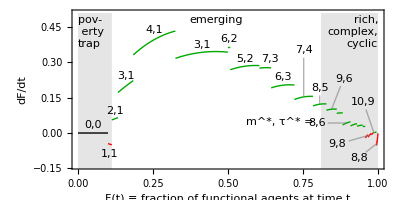

```mathematica
Module[{increasingColor=Darker@Green,decreasingColor=Red,stationaryColor=Black,fontOffset=6,fontMultiplier=15,fontExponent=1,plots,fontSize=10,ODEs=ODEsα0p1β0p4L1p5,font="Arial",imageSize= 3.41/3.44 {8.7 *72/2.54},aspectRatio=.5,L=1.5,displacement,callout,bestResponses=bestResponsesα0p1β0p4Fixedspacing0p0001,styleLabel,createLabel,plotRange,columnSpacings=.3,spaceBetweenMτ=Spacer[1.2]},

plots=(Plot[#ODE,#Fiterator,

PlotStyle->{Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,stationaryColor],AbsoluteThickness[1]}

]&)/@ODEs;

styleLabel[lbl_,width_]:=Style[lbl,{FontFamily->"Times"}];

displacement[br_,FdotMidPoint_]:={0,0.02}
+
Which[
br[[1]]≥8||br=={7,3},{0,(.05+br[[2]]*.01) Sign[FdotMidPoint]}
,True,{0,0}
]
+If[br=={9,6},{0,.07},0]
+If[br=={10,7},{-.05,-.2},0]
;

callout[label_,pos_,pointPos_]:={Inset[label,pos],Line[pos,pointPos]};
createLabel=Module[{positionArrowhead,positionLabel,displaceLabelPosition,d=.032},

If[
(* Show labels for these portions of the ODE *)
#Fmidpoint≤.85||#bestResponse=={9,8}||#bestResponse=={8,8}||#bestResponse=={8,6}||(#bestResponse=={10,9}&&#FdotMidPoint>0),


positionArrowhead={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};
positionLabel={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};

displaceLabelPosition={0,0};
Which[
#bestResponse=={0,0},displaceLabelPosition+={0,d};,
#bestResponse=={1,1},displaceLabelPosition+={0,-.04};,
#bestResponse=={2,1}||#bestResponse=={5,2},displaceLabelPosition+={0,d};,
#bestResponse=={3,1}&&#Fmidpoint<.2,displaceLabelPosition+={0,.042};,
#bestResponse=={3,1}&&#Fmidpoint>.2,displaceLabelPosition+={0,d};,
#bestResponse=={4,1},displaceLabelPosition={0,.04};,
#bestResponse=={7,3},displaceLabelPosition={0.015,.035};,
#bestResponse=={6,2},displaceLabelPosition={0.0,.035};,
#bestResponse=={6,3},displaceLabelPosition={0 0.015,.035};,
#bestResponse=={7,4},displaceLabelPosition={0,.2};,
#bestResponse=={8,5},displaceLabelPosition={0,.07};,
#bestResponse=={9,6},displaceLabelPosition={.04,.13};,
#bestResponse=={10,7},displaceLabelPosition={0,.15};,
#bestResponse=={8,6},displaceLabelPosition={-.1,0};,
#bestResponse=={9,7},displaceLabelPosition={0,.1};,
#bestResponse=={10,8},displaceLabelPosition={0,.15};,
#bestResponse=={11,9},displaceLabelPosition={0,.08};,
#bestResponse=={8,7},displaceLabelPosition={-.1,0};,
#bestResponse=={9,8},displaceLabelPosition={-.11,-0.04};,
#bestResponse=={10,9}&&#FdotMidPoint<0,displaceLabelPosition={-.05,-0.1};,
#bestResponse=={10,9}&&#FdotMidPoint>0,displaceLabelPosition={-.035,0.13};,
#bestResponse=={10,10}&&#FdotMidPoint<0,displaceLabelPosition={-.06,-0.15};,
#bestResponse=={8,8}&&#FdotMidPoint<0,displaceLabelPosition={-.06,-0.06};

];

positionLabel+=displaceLabelPosition;

{

Inset[
Row[
Style[#,{FontFamily->font}]&/@
Join[
If[False,
{
Style["m^*",Gray],Style[",",Gray],
spaceBetweenMτ,
Style["τ^*",Gray],
spaceBetweenMτ,
 Style["=",Gray],
spaceBetweenMτ
}
,
{}],
{
Style[#["bestResponse"]⟦1⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],Style[",",Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],
spaceBetweenMτ,
Style[#["bestResponse"]⟦2⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]]
}]
],
positionLabel]

,
If[Norm[positionLabel-positionArrowhead]>.05,
{Gray,Opacity[.6],Line[
{positionLabel+.033 Normalize[positionArrowhead-positionLabel]
+If[#bestResponse=={9,8},.01 Normalize[positionArrowhead-positionLabel],0]
+If[#bestResponse=={8,6},.004 Normalize[positionArrowhead-positionLabel],0]
,positionArrowhead}]}
,
Nothing
]
}
,
Nothing

]

]

&;

plotRange={-.14,.51};

Show[
plots
,FrameLabel->(Style[#,{FontFamily->font,FontSize->fontSize}]&/@{"F(t) ≡ fraction of functional agents at time t","dF/dt"}),
ImageSize->imageSize,
PlotRange->plotRange,
Filling->Axis,PlotRangeClipping->True,PlotRangePadding->{{0.0,0.003},{0,0}},FrameTicksStyle->Directive[FontFamily->font,Gray],
Prolog->
{
{{Opacity[.1],Rectangle[{0,-1},{SelectFirst[bestResponses,Chop[#["Fdot"]/."L"->L]>0&]["F"],plotRange⟦2⟧}]}},
{{Opacity[.1],Rectangle[{.81,-1},{1,plotRange⟦2⟧}]}}
},
AspectRatio->aspectRatio,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
Epilog->Join[createLabel/@ODEs,{Inset[
Column[{
Style["pov-",{FontFamily->font,FontSize->fontSize}],Style[" erty",{FontFamily->font,FontSize->fontSize}],
Style["trap",{FontFamily->font,FontSize->fontSize}]
},Alignment->Left,Spacings->columnSpacings]
,{0,.5},{-1.25,1}],
Inset[
Column[
{Style["rich,",{FontFamily->font,FontSize->fontSize}],
Style["complex,",{FontFamily->font,FontSize->fontSize}],
Style["cyclic",{FontFamily->font,FontSize->fontSize}]}
,Spacings->columnSpacings,Alignment->Center]
,{1,.5},{1.,1}],

Inset[
Column[
{Style["emerging",{FontFamily->font,FontSize->fontSize}]}
,Spacings->columnSpacings,Alignment->Center]
,{0.4613508326896292,.5},{0,1}],

Inset[
Row[Style[#,{FontFamily->font}]&/@{
Style["m^*",FontSize->fontSize,Black],
Style[", ",FontSize->fontSize,Black],
Style["τ^*",FontSize->fontSize,Black],
Style[" = ",FontSize->fontSize,Black]
}]
,{.672,.045}
]

}]
]
]
```

```mathematica
Export[FileNameJoin[{"figures","figure3.pdf"}],%];
```

## Figure 4

Here, agents use a strategy that requires s=2 more inputs than they would have chosen given the reliability F(t) of their potential inputs: they use the strategy (m^*+2,τ^*+2), where (m^*,τ^*) is the best response.

### compute best responses with s=2 extra inputs

The variable s is the number of extra inputs:

```mathematica
Module[{s=2},
bestResponsesα0p1β0p4Fixedspacing0p0001With2ExtraInputs=
<|"α"->#α,"β"->#β,"F"->#F,"bestResponse"->#bestResponse+{s,s},
"Fdot"->
(-#F "L"+probSuccess[#bestResponse+{s,s},#F]+#F (-1+"L") probSuccess[#bestResponse+{s,s},#F]) Boole[#bestResponse[[2]]+s>0]
|>&/@bestResponsesα0p1β0p4Fixedspacing0p0001;
]
```

#### Save the result to the hard disk:

```mathematica
bestResponsesα0p1β0p4Fixedspacing0p0001With2ExtraInputs>>
(FileNameJoin[{"data","bestResponses_alpha0p1_beta0p4_fixedspacing0p0001_2extraInputs"}]);
```

#### Load it from the disk:

```mathematica
bestResponsesα0p1β0p4Fixedspacing0p0001With2ExtraInputs<<
(FileNameJoin[{"data","bestResponses_alpha0p1_beta0p4_fixedspacing0p0001_2extraInputs"}]);
```

### compute the ODEs

Note that here the key “bestResponse” points to the best response + {2, 2}.

```mathematica
ODEsα0p1β0p4L1p5With2ExtraInputs=Module[{s=2,L=1.5,bestResponses=bestResponsesα0p1β0p4Fixedspacing0p0001With2ExtraInputs},
((Association@
{
"ODE"->(F (L (-1+P)-P)+P) * Boole[τ>0]
/.{P->Probability[S≥τ,S\[Distributed]BinomialDistribution[m,F]]}
/.{m->#1["bestResponse"][[1]],τ->#1["bestResponse"][[2]]}
,
"Fiterator"->{F,#1["F"],#2["F"]},
"Fmidpoint"->(#1["F"]+#2["F"])/2.0,
"bestResponse"->#1["bestResponse"],
"FdotMidPoint"->#Fdot/.{"L"->L,F-> (#1["F"]+#2["F"])/2}}&)@@@(Drop[#,{2,-2}]&/@Select[SplitBy[bestResponses,{#bestResponse,Sign[#Fdot/."L"->L]}&],Length[#]≥2&]))];
```

#### Save the results to the hard disk:

```mathematica
ODEsα0p1β0p4L1p5With2ExtraInputs>>(FileNameJoin[{"data","ODEs_alpha0p1_β0p4_L1p5_2extraInputs"}]);
```

#### Load the results from the hard disk:

```mathematica
(<<(FileNameJoin[{"data","ODEs_alpha0p1_β0p4_L1p5_2extraInputs"}]))
```

{<|ODE→F^2+F (-F^2+1.5 (-1+F^2)),Fiterator→{F,0.0001,0.1},Fmidpoint→0.05005,bestResponse→{2,2},FdotMidPoint→-0.00014999|>,<|ODE→F^3+F (-F^3+1.5 (-1+F^3)),Fiterator→{F,0.1001,0.1127},Fmidpoint→0.1064,bestResponse→{3,3},FdotMidPoint→-0.149097|>,<|ODE→F (1.5 (-1+BetaRegularized[F,3,2])-BetaRegularized[F,3,2])+BetaRegularized[F,3,2],Fiterator→{F,0.1128,0.133},Fmidpoint→0.1229,bestResponse→{4,3},FdotMidPoint→-0.163648|>,<|ODE→F (1.5 (-1+BetaRegularized[F,3,3])-BetaRegularized[F,3,3])+BetaRegularized[F,3,3],Fiterator→{F,0.1331,0.1841},Fmidpoint→0.1586,bestResponse→{5,3},FdotMidPoint→-0.179255|>,<|ODE→F (1.5 (-1+BetaRegularized[F,3,4])-BetaRegularized[F,3,4])+BetaRegularized[F,3,4],Fiterator→{F,0.1842,0.3246},Fmidpoint→0.2544,bestResponse→{6,3},FdotMidPoint→-0.188457|>,<|ODE→F (1.5 (-1+BetaRegularized[F,3,3])-BetaRegularized[F,3,3])+BetaRegularized[F,3,3],Fiterator→{F,0.3247,0.4996},Fmidpoint→0.41215,bestResponse→{5,3},FdotMidPoint→-0.257772|>,<|ODE→F (1.5 (-1+BetaRegularized[F,4,5])-BetaRegularized[F,4,5])+BetaRegularized[F,4,5],Fiterator→{F,0.4997,0.5074},Fmidpoint→0.50355,bestResponse→{8,4},FdotMidPoint→0.0454325|>,<|ODE→F (1.5 (-1+BetaRegularized[F,4,4])-BetaRegularized[F,4,4])+BetaRegularized[F,4,4],Fiterator→{F,0.5075,0.5834},Fmidpoint→0.54545,bestResponse→{7,4},FdotMidPoint→-0.11381|>,<|ODE→F (1.5 (-1+BetaRegularized[F,4,4])-BetaRegularized[F,4,4])+BetaRegularized[F,4,4],Fiterator→{F,0.5835,0.6045},Fmidpoint→0.594,bestResponse→{7,4},FdotMidPoint→0.000100287|>,<|ODE→F (1.5 (-1+BetaRegularized[F,5,5])-BetaRegularized[F,5,5])+BetaRegularized[F,5,5],Fiterator→{F,0.6046,0.6437},Fmidpoint→0.62415,bestResponse→{9,5},FdotMidPoint→0.0606733|>,<|ODE→F (1.5 (-1+BetaRegularized[F,5,4])-BetaRegularized[F,5,4])+BetaRegularized[F,5,4],Fiterator→{F,0.6438,0.6739},Fmidpoint→0.65885,bestResponse→{8,5},FdotMidPoint→-0.0496023|>,<|ODE→F (1.5 (-1+BetaRegularized[F,5,4])-BetaRegularized[F,5,4])+BetaRegularized[F,5,4],Fiterator→{F,0.674,0.7212},Fmidpoint→0.6976,bestResponse→{8,5},FdotMidPoint→0.0000443021|>,<|ODE→F (1.5 (-1+BetaRegularized[F,6,4])-BetaRegularized[F,6,4])+BetaRegularized[F,6,4],Fiterator→{F,0.7213,0.7358},Fmidpoint→0.72855,bestResponse→{9,6},FdotMidPoint→-0.0250447|>,<|ODE→F (1.5 (-1+BetaRegularized[F,6,4])-BetaRegularized[F,6,4])+BetaRegularized[F,6,4],Fiterator→{F,0.7359,0.7831},Fmidpoint→0.7595,bestResponse→{9,6},FdotMidPoint→0.0000307273|>,<|ODE→F (1.5 (-1+BetaRegularized[F,7,4])-BetaRegularized[F,7,4])+BetaRegularized[F,7,4],Fiterator→{F,0.7832,0.8279},Fmidpoint→0.80555,bestResponse→{10,7},FdotMidPoint→0.00487328|>,<|ODE→F (1.5 (-1+BetaRegularized[F,8,4])-BetaRegularized[F,8,4])+BetaRegularized[F,8,4],Fiterator→{F,0.828,0.8624},Fmidpoint→0.8452,bestResponse→{11,8},FdotMidPoint→0.0236765|>,<|ODE→F (1.5 (-1+BetaRegularized[F,9,4])-BetaRegularized[F,9,4])+BetaRegularized[F,9,4],Fiterator→{F,0.8625,0.8822},Fmidpoint→0.87235,bestResponse→{12,9},FdotMidPoint→0.0359283|>,<|ODE→F (1.5 (-1+BetaRegularized[F,8,3])-BetaRegularized[F,8,3])+BetaRegularized[F,8,3],Fiterator→{F,0.8823,0.9012},Fmidpoint→0.89175,bestResponse→{10,8},FdotMidPoint→-0.0319752|>,<|ODE→F (1.5 (-1+BetaRegularized[F,8,3])-BetaRegularized[F,8,3])+BetaRegularized[F,8,3],Fiterator→{F,0.9013,0.9084},Fmidpoint→0.90485,bestResponse→{10,8},FdotMidPoint→0.0000990048|>,<|ODE→F (1.5 (-1+BetaRegularized[F,9,3])-BetaRegularized[F,9,3])+BetaRegularized[F,9,3],Fiterator→{F,0.9085,0.9169},Fmidpoint→0.9127,bestResponse→{11,9},FdotMidPoint→-0.0136761|>,<|ODE→F (1.5 (-1+BetaRegularized[F,9,3])-BetaRegularized[F,9,3])+BetaRegularized[F,9,3],Fiterator→{F,0.917,0.9301},Fmidpoint→0.92355,bestResponse→{11,9},FdotMidPoint→0.0000164921|>,<|ODE→F (1.5 (-1+BetaRegularized[F,10,3])-BetaRegularized[F,10,3])+BetaRegularized[F,10,3],Fiterator→{F,0.9302,0.9489},Fmidpoint→0.93955,bestResponse→{12,10},FdotMidPoint→0.00173016|>,<|ODE→F (1.5 (-1+BetaRegularized[F,11,3])-BetaRegularized[F,11,3])+BetaRegularized[F,11,3],Fiterator→{F,0.949,0.9573},Fmidpoint→0.95315,bestResponse→{13,11},FdotMidPoint→0.0129416|>,<|ODE→F (1.5 (-1+BetaRegularized[F,9,2])-BetaRegularized[F,9,2])+BetaRegularized[F,9,2],Fiterator→{F,0.9574,0.9665},Fmidpoint→0.96195,bestResponse→{10,9},FdotMidPoint→-0.0535888|>,<|ODE→F (1.5 (-1+BetaRegularized[F,10,2])-BetaRegularized[F,10,2])+BetaRegularized[F,10,2],Fiterator→{F,0.9666,0.9776},Fmidpoint→0.9721,bestResponse→{11,10},FdotMidPoint→-0.041089|>,<|ODE→F (1.5 (-1+BetaRegularized[F,11,2])-BetaRegularized[F,11,2])+BetaRegularized[F,11,2],Fiterator→{F,0.9777,0.9883},Fmidpoint→0.983,bestResponse→{12,11},FdotMidPoint→-0.0198226|>,<|ODE→F (1.5 (-1+BetaRegularized[F,12,2])-BetaRegularized[F,12,2])+BetaRegularized[F,12,2],Fiterator→{F,0.9884,0.9908},Fmidpoint→0.9896,bestResponse→{13,12},FdotMidPoint→-0.00280502|>,<|ODE→F (1.5 (-1+BetaRegularized[F,12,2])-BetaRegularized[F,12,2])+BetaRegularized[F,12,2],Fiterator→{F,0.9909,0.995},Fmidpoint→0.99295,bestResponse→{13,12},FdotMidPoint→0.0000636981|>,<|ODE→F^10+F (-F^10+1.5 (-1+F^10)),Fiterator→{F,0.9951,0.9966},Fmidpoint→0.99585,bestResponse→{10,10},FdotMidPoint→-0.0668829|>,<|ODE→F^11+F (-F^11+1.5 (-1+F^11)),Fiterator→{F,0.9967,0.9989},Fmidpoint→0.9978,bestResponse→{11,11},FdotMidPoint→-0.0502015|>,<|ODE→F^12+F (-F^12+1.5 (-1+F^12)),Fiterator→{F,0.999,0.9999},Fmidpoint→0.99945,bestResponse→{12,12},FdotMidPoint→-0.0168954|>}

```mathematica
ODEsα0p1β0p4L1p5With2ExtraInputs=(<<(FileNameJoin[{"data","ODEs_alpha0p1_β0p4_L1p5_2extraInputs"}]));
```

### plot figure 4

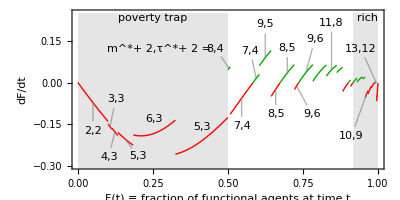

```mathematica
Module[{increasingColor=Darker@Green,decreasingColor=Red,stationaryColor=Black,fontOffset=6,fontMultiplier=15,fontExponent=1,plots,fontSize=10,ODEs=ODEsα0p1β0p4L1p5With2ExtraInputs,font="Arial",imageSize= 3.41/3.44 {8.7 *72/2.54},aspectRatio=.5,L=1.5,displacement,callout,bestResponses=bestResponsesα0p1β0p4Fixedspacing0p0001,styleLabel,createLabel,plotRange,columnSpacings=.2,povertyTrapRightEndpoint,richLeftEndpoint,shiftmτLabel={-.02,.03},spaceBetweenMτ=Spacer[1.2]},

plots=(Plot[#ODE,#Fiterator,

PlotStyle->{Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,stationaryColor],AbsoluteThickness[1]}

]&)/@ODEs;

povertyTrapRightEndpoint=SelectFirst[ODEs,#FdotMidPoint>0&]["Fiterator"]⟦2⟧;
richLeftEndpoint=Select[Reverse[ODEs],#FdotMidPoint>0&]⟦4⟧["Fiterator"]⟦2⟧;

styleLabel[lbl_,width_]:=Style[lbl,{FontFamily->"Times"}];

displacement[br_,FdotMidPoint_]:={0,0.02}
+
Which[
br[[1]]≥8||br=={7,3},{0,(.05+br[[2]]*.01) Sign[FdotMidPoint]}
,True,{0,0}
]
+If[br=={9,6},{0,.07},0]
+If[br=={10,7},{-.05,-.2},0]
;

callout[label_,pos_,pointPos_]:={Inset[label,pos],Line[pos,pointPos]};
createLabel=Module[{positionArrowhead,positionLabel,displaceLabelPosition,d=.032},

If[
(* Show labels for these portions of the ODE *)
(#Fmidpoint≤.85||#bestResponse=={10,9}||(#bestResponse=={13,12}&&#FdotMidPoint>0))&&Not[#bestResponse=={10,7}],


positionArrowhead={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};
positionLabel={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};

displaceLabelPosition={0,0};
(*displaceLabelPosition+={0,.1};*)
displaceLabelPosition+=If[#FdotMidPoint>0,{0,.05},{0,-.05}];
displaceLabelPosition+=
Which[
#bestResponse=={2,2},{0,-.05},
#bestResponse=={3,3},{.02,.15},
#bestResponse=={4,3},{-.02,-.04},
#bestResponse=={5,3}&&#Fmidpoint<.3,{.04,-.01},
#bestResponse=={5,3}&&#Fmidpoint>.3,{0,.1},
#bestResponse=={6,3},{0,.10},
#bestResponse=={7,4}&&#FdotMidPoint<0,{0,-.05},
#bestResponse=={7,4}&&#FdotMidPoint>0,{-.02,.05},
#bestResponse=={8,4},{-.025,-.01}+shiftmτLabel,
#bestResponse=={8,5},{0,Sign[#FdotMidPoint] .04},
#bestResponse=={9,5},{0,.07},
#bestResponse=={9,6}&&#FdotMidPoint>0,{.03,.07},
#bestResponse=={9,6}&&#FdotMidPoint<0,{.05,-.05},
#bestResponse=={13,12}&&#FdotMidPoint>0,{-.05,0.07},
#bestResponse=={10,9}&&#FdotMidPoint<0,{-.05,-0.1},
#bestResponse=={11,8},{0,.12},
True,{0,0}
];

positionLabel+=displaceLabelPosition;

{
Inset[
Row[
Style[#,{FontFamily->font}]&/@
Join[
If[False,
{
Style["m^*",Gray],
Style[",",Gray],
Style["τ^*",Gray],
Style["= ",Gray]
}
,
{}],
{
Style[#["bestResponse"]⟦1⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],Style[",",Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],
spaceBetweenMτ,
Style[#["bestResponse"]⟦2⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]]
}]
],
positionLabel]

,
(* whether to show a gray line *)
If[Norm[positionLabel-positionArrowhead]>.07,
{Gray,Opacity[.6],Line[
{positionLabel+.033 Normalize[positionArrowhead-positionLabel]
,positionArrowhead}]}
,
Nothing
]
}
,
Nothing

]

]&;

plotRange={-.30,.25};

Show[
plots
,FrameLabel->(Style[#,{FontFamily->font,FontSize->fontSize}]&/@{"F(t) ≡ fraction of functional agents at time t","dF/dt"(*"Ḟ ≡ dF/dt"*)}),
ImageSize->imageSize,
PlotRange->plotRange,
Filling->Axis,PlotRangeClipping->True,PlotRangePadding->{{0.0,0.003},{0,0}},FrameTicksStyle->Directive[FontFamily->font,Gray],
Prolog->
{
{{Opacity[.1],Rectangle[{0,-1},{povertyTrapRightEndpoint,plotRange⟦2⟧}]}},
{{Opacity[.1],Rectangle[{richLeftEndpoint,-1},{1,plotRange⟦2⟧}]}}
},
AspectRatio->aspectRatio,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
Epilog->Join[createLabel/@ODEs,{Inset[
Column[{
Style["poverty trap",{FontFamily->font,FontSize->fontSize}]
},Alignment->Center,Spacings->columnSpacings]
,{povertyTrapRightEndpoint/2,(*-0.18*)plotRange[[2]]},{0,1.2}],
Inset[
Column[
{Style["rich",{FontFamily->font,FontSize->fontSize}]}
,Spacings->columnSpacings,Alignment->Center]
,{1,plotRange[[2]]},{1.,1.2}],

Inset[
Row[Style[#,{FontFamily->font,Black}]&/@{
Style["m^*+ 2",FontSize->fontSize],Style[",",FontSize->fontSize],
spaceBetweenMτ,
Style["τ^*+ 2",FontSize->fontSize],
Style[" = ",FontSize->fontSize]
}]
,{.29,.091}+shiftmτLabel
]

}]
]
]
```

```mathematica
Export[FileNameJoin[{"figures","figure4.pdf"}],%];
```